# Tight-binding electronic structure of graphene

We illustrate the generation of effective tight-binding Hamiltonians in the two-center Slater-Koster formalism for the 2-dimensional carbon allotrope graphene.

GTClusterpaclet:GroupTheory/ref/GTClusterGroupTheory Package Symbol | constructs a spherical cluster crystal structure.
GTShellspaclet:GroupTheory/ref/GTShellsGroupTheory Package Symbol | performs a reordering of a cluster of atoms into shells
GTTBHamiltonianpaclet:GroupTheory/ref/GTTBHamiltonianGroupTheory Package Symbol | constructs a k-dependent tight-binding Hamiltonian □
GTHamiltonianPlotpaclet:GroupTheory/ref/GTHamiltonianPlotGroupTheory Package Symbol | plots the structure of a Hamiltonian
GTBZPathpaclet:GroupTheory/ref/GTBZPathGroupTheory Package Symbol | generates a standard path in the Brillouin zone
GTBandStructurepaclet:GroupTheory/ref/GTBandStructureGroupTheory Package Symbol | calculates and plots the band structure for a given Hamiltonian
GTBandspaclet:GroupTheory/ref/GTBandsGroupTheory Package Symbol | calculates the lowest band energies for a given Hamiltonian

Graphene crystallizes in a 2-dimensional honeycomb lattice with two atoms in the primitive unit cell. In GTPack, structures are specified as a list, where the list contains the name of the structure and a prototype, four different names for the space group (Pearson symbol, Strukturbericht designation, international notation, and space group number), the lattice, and the sites containing the atom name and the atom position. Note that the first five information are optional and not important for the generation of the tight-binding model. The structure itself can be plotted using GTPlotStructure2Dpaclet:GroupTheory/ref/GTPlotStructure2DGroupTheory Package Symbol. In our example we choose the lattice constant to be a = 1 a.u. and plot the structure within a radius of 5 a.u..

```mathematica
Needs["GroupTheory`"]
```

```mathematica
hcp={{"C","Honeycomb"},"hP1","A_f","P6/mmm",191,
{{Sqrt[3]a,0,0},{Sqrt[3]a/2,3a/2,0},{0,0,0}},
{{{0,0,0},"C1"},{{0,-a,0},"C2"}},{a->240}};
```

```mathematica
GTPlotStructure2D[hcp,5,GOLattice->{a->1}]
```

61 atoms

Atoms in cluster: {{C1,31},{C2,30}}

-Graphics-

For the construction of the tight-binding model it is necessary to construct a real space cluster. This cluster is reordered into different shells corresponding to nearest neighbor, next nearest neighbor, next next nearest neighbor interactions, etc. The respective commands to do so are GTClusterpaclet:GroupTheory/ref/GTClusterGroupTheory Package Symbol and GTShellspaclet:GroupTheory/ref/GTShellsGroupTheory Package Symbol. Originating from each of the two carbon atoms in the unit cell we choose to construct a cluster of a radius of 3 a.u. about both atoms. Using the option GOTbLatticepaclet:GroupTheory/ref/GOTbLatticeGroupTheory Package Symbol one can specify which interaction are to be taken into account. Here we choose a nearest neighbor tight-binding model, where only the first shell of the two nonequivalent carbon atoms is taken into account. We furthermore set the onsite interaction to zero. Using GOPositionpaclet:GroupTheory/ref/GOPositionGroupTheory Package Symbol we set the algorithm to work in relative coordinates.

```mathematica
cl=GTCluster[hcp,3,GOLattice->{a->1}];
bas0=hcp[[7]] /.{a->1}; shells={2,2};
```

25 atoms

Atoms in cluster: {{C1,13},{C2,12}}

```mathematica
lat=GTShells[cl,bas0,shells,GOVerbose->True,
GOTbLattice->{{"C1,C1",{0}}, {"C2,C2",{0}},{"C1,C2",{1}}},
GOPosition->"Relative"];
```

Basis | dist | Atoms | dist | Atoms
C1 | 1 | {{C1,1},{C2,3}} | √3 | {{C1,7},{C2,3}}
C2 | 1 | {{C1,3},{C2,1}} | √3 | {{C1,3},{C2,7}}

Using the information for the corresponding shells as well as an orbital basis, a tight-binding Hamiltonian is constructed using GTTbHamiltonianpaclet:GroupTheory/ref/GTTbHamiltonianGroupTheory Package Symbol. The orbital basis is specified as a list containing : i) the name of the site or type; ii) the number of atoms of this type; iii) a list of angular momenta to be taken into account. In our example we consider s–(l = 0) and p - orbitals (l = 1) only, so the angular momentum information is {0, 1}. To obtain a better overview of the non-zero matrix elements of the Hamiltonian, GTHamiltonianPlotpaclet:GroupTheory/ref/GTHamiltonianPlotGroupTheory Package Symbol is used.

```mathematica
bas={{"C1",1,{0,1}},{"C2",1,{0,1}}};
hamc=GTTbHamiltonian[bas,lat];
GTHamiltonianPlot[hamc,bas]
```

| s | p_y | p_z | p_x | s | p_y | p_z | p_x
s |   |   |   |   |   |   |   |  
p_y |   |   |   |   |   |   |   |  
p_z |   |   |   |   |   |   |   |  
p_x |   |   |   |   |   |   |   |  
s |   |   |   |   |   |   |   |  
p_y |   |   |   |   |   |   |   |  
p_z |   |   |   |   |   |   |   |  
p_x |   |   |   |   |   |   |   |

As can be verified, all orbitals with in - plane components hybridize, i.e., s -, p_x -, and p_y - orbitals. However, the p_z-orbitals do not hybridize with any of the other orbitals, leading to a 2x2 sub-matrix which is extracted from the full Hamiltonian in the following. Furthermore, we apply GTBZPathpaclet:GroupTheory/ref/GTBZPathGroupTheory Package Symbol to obtain a standard path for the band structure calculation.

```mathematica
hpp={{hamc[[3,3]],hamc[[3,7]]},{hamc[[7,3]],hamc[[7,7]]}};
```

```mathematica
kp=GTBZPath["Honeycomb"]
```

{{{-2/(3 √3),0,0},{0,0,0},{1/(2 √3),-1/6,0},{2/(3 √3),0,0}},{K',Γ,M,K}}

The final band structure plot is obtained using the command GTBandStructurepaclet:GroupTheory/ref/GTBandStructureGroupTheory Package Symbol. We set the on-site energies to zero and choose a value of 1 (in arbitrary units) for the nearest neighbor hopping strength. GTBandStructurepaclet:GroupTheory/ref/GTBandStructureGroupTheory Package Symbol requires the Hamiltonian, the high-symmetry points of the Brillouin zone path, the number of mesh points used along each segment of the Brillouin zone path, as well as the number of bands to be plotted.

```mathematica
hamrule={("(pp0)")^("C1")->0,("(pp0)")^("C2")->0,Subscript["(ppπ)", 1]^("C1,C2")->1.};
hparm=hpp /. hamrule;
```

Maximum Abscissa = 0.910684

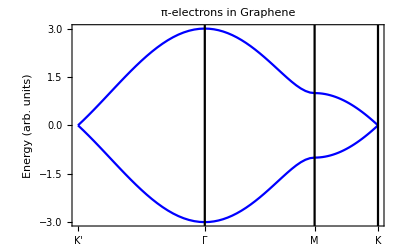

```mathematica
GTBandStructure[hparm,kp,25,2,Joined->True,
FrameLabel->{" ","Energy (arb. units)"}, 
PlotLabel->"π-electrons in Graphene"]
```

For large Hamiltonians it can be useful to store the calculated band structure as well as the wave function coefficients. To do so, GTBandspaclet:GroupTheory/ref/GTBandsGroupTheory Package Symbol can be used, specifying the option GOStorepaclet:GroupTheory/ref/GOStoreGroupTheory Package Symbol. GTBandspaclet:GroupTheory/ref/GTBandsGroupTheory Package Symbol requires the actual k-points, which we obtain from the high-symmetry points using GTBZLinespaclet:GroupTheory/ref/GTBZLinesGroupTheory Package Symbol.

```mathematica
kpl=GTBZLines[kp,{25,25,25,25}]//N;
bands=GTBands[hparm,kpl,2,GOEigenvectors->True,
GOStore->{"graphene.bnd","graphene.wf"}];
```

Write to file: graphene.bnd

Write to file: graphene.wf

| Related Guides
▪W. Hergert, R. M. Geilhufe, Group Theory in Solid State Physics and Photonics: Problem Solving with Mathematica, Wiley-VCH, ISBN: 978-3-527-41133-7 (2018).http://gtpack.org/book/